### Plot for problem 5.5, anharmonic oscillator.

```mathematica
<<peeters` ;
peeters`setGitDir[ "blogit" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit

ⅇ^(ⅈ t)-0.0833333 ⅇ^(2 ⅈ t)+0.00520833 ⅇ^(3 ⅈ t)-0.000115741 ⅇ^(4 ⅈ t)

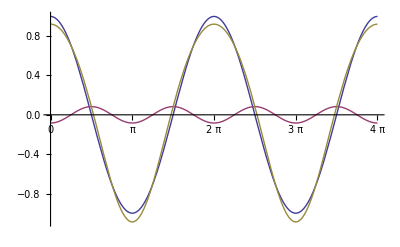

```mathematica
Clear[s]
s = Module[{f, g, omega, m, a, r},
f = 1 ;
g = 0.5 ;
m = 1 ;
omega = Sqrt[f/m] ;
r = g/(2 m omega^2) ;
a = { 1, -r/3, r^2/12, -r^3/135} ;
u[t_] = Sum[a[[n]] E^(I n omega t), {n, 4} ] ;

{u[t], 
Plot[{Re[E^(I omega t)], Re[a[[2]] E^(I 2 omega t)], Re[u[t]]}
, {t, 0, 4 Pi}
, Ticks -> { Table[ m Pi/2, {m, 0, 8}], Automatic }
] }
] ;

s[[1]] // TraditionalForm
s[[2]]
```

```mathematica
peeters`exportForLatex["anharmonicOscFig1", s[[2]] ]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/anharmonicOscFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/anharmonicOscFig1pn.png}